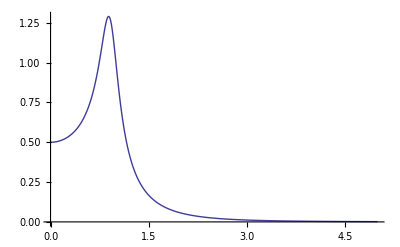

```mathematica
Plot[1/Sqrt[((ω^4-4ω^2+2)^2+(3ω-3ω^3)^2)],{ω,0,5}]
```

```mathematica
FindMaximum[1/Sqrt[((ω^4-4ω^2+2)^2+(3ω-3ω^3)^2)],{ω,0,2}]
```

{1.2902,{ω→0.888663}}

```mathematica
Rea[ω_]=((1-ω^2)(ω^4-4ω^2+2)+ω*(3ω-3ω^3))/((ω^4-4ω^2+2)^2+(3ω-3ω^3)^2)
```

(ω (3 ω-3 ω^3)+(1-ω^2) (2-4 ω^2+ω^4))/((3 ω-3 ω^3)^2+(2-4 ω^2+ω^4)^2)

```mathematica
Ima[ω_]=(ω*(ω^4-4ω^2+2)-(1-ω^2)(3ω-3ω^3))/((ω^4-4ω^2+2)^2+(3ω-3ω^3)^2)
```

(-(1-ω^2) (3 ω-3 ω^3)+ω (2-4 ω^2+ω^4))/((3 ω-3 ω^3)^2+(2-4 ω^2+ω^4)^2)

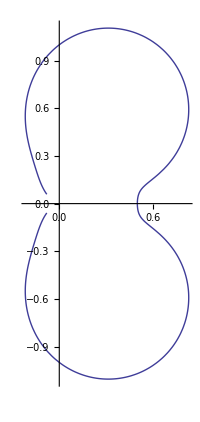

```mathematica
ParametricPlot[{Rea[ω],Ima[ω]},{ω,-3,3}]
```

```mathematica
FindMaximum[Im[ω],{ω,0,1}]
```

{1.10508,{ω→-0.941943}}

```mathematica
Rea[0]
```

1/2

```mathematica
F1[β_]=-(β^2+3)/(β+1)^2
```

(-3-β^2)/(1+β)^2

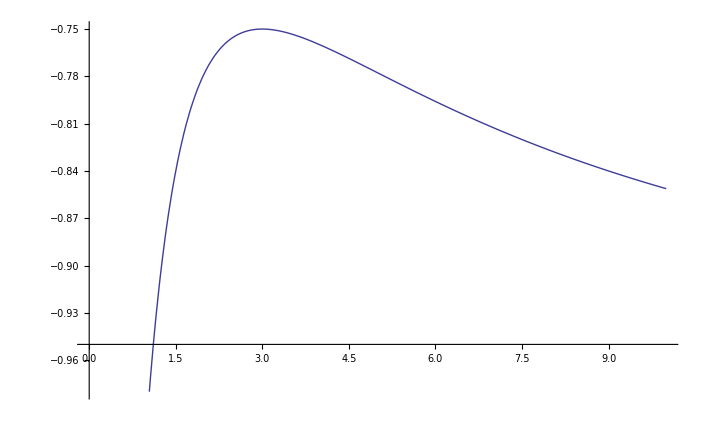

```mathematica
Plot[F1[β],{β,0,10}]
```

```mathematica
Maximize[F1[β],β]
```

{-3/4,{β→3}}

```mathematica
Limit[F1[β],β->+Infinity]
```

-1